```mathematica
(*constants*)
nm=10^-9;(*nm unit weight*)
c=299792458;(*speed of light in m/s*)
eV=1.602176634*10^-19;
hbar=1.0545718*10^-34;(*reduced Planck constant*)
eC=1.60217662*10^-19;(*electron charge*)
me=9.10938356*10^-31;(*electron mass*)
a0=5.29177210903*10^-11;(*Bohr radius*)
eps0=8.8541878128*10^-12;(*free space permittivity*)
```

```mathematica
(*parameteres for Drude metal (see Maier 1.27) and non-local case (see https://pubs.acs.org/doi/10.1021/nn406153k)*)
metal=TableForm[{{4,1,0.066},{3.01,8,0.135}},TableHeadings->{{"sodium","gold"},{"Wigner-Seitz radius","esp infty","damping rate"}}];
mtype=Input["set the metal; 1 for Na, 2 for Au"];
rs=metal[[1,mtype]][[1]];
nb=(4/3*Pi*rs^3)^-1/a0^3;(*Bulk electron density*)(*omegaP=Sqrt[eC^2*nb/me/eps0];*)
omegaP=eC*Sqrt[nb/me/eps0];(*plasma frequency in rad/s*)
epsINF=metal[[1,mtype]][[2]];(*dielectric constant to account for the background ion cores*)
gammaD=metal[[1,mtype]][[3]];(*damping parameter in eV*)
gammaD=gammaD*eV/hbar;(*damping parameter in rad/s*)
kF=(3*Pi^2*nb)^(1/3);(*Fermi angular wave number*)
vF=kF*(hbar/me)(*Fermi velocity*);
betaF=Sqrt[1/3]*vF;
```

```mathematica
(*relative permittivity -> dependence should be in wavelenghts measured in nm*)
eps1=1;(*medium is Air with permittivity equal to 1*)
eps2[lmbd_]:=epsINF-omegaP^2/(Power[2*Pi*c/(lmbd*nm),2]+I*gammaD*(2*Pi*c/(lmbd*nm)))
(*lmbd -> wavelenght in nm*)
```

```mathematica
(*variables*)
k1[lmbd_]:=Sqrt[eps1]*2*Pi/(lmbd*nm);(*wave number for the medium in 1/m*)
k2[lmbd_]:=Sqrt[eps2[lmbd]]*2*Pi/(lmbd*nm);(*wave number for the sphere in 1/m*)
k2nl[lmbd_]:=omegaP/betaF*Sqrt[eps2[lmbd]/(epsINF*(epsINF-eps2[lmbd]))];(*non-local wave number for the sphere in 1/m*)
rho1[lmbd_,a_]:=k1[lmbd]*a*nm;
rho2[lmbd_,a_]:=k2[lmbd]*a*nm;
rho2nl[lmbd_,a_]:=k2nl[lmbd]*a*nm;
(*a is the radius of the sphere*)
```

```mathematica
(*special functions*)
sphB1[mod_,a_,lmbd_]:=SphericalBesselJ[mod,rho1[lmbd,a]];
sphB2[mod_,a_,lmbd_]:=SphericalBesselJ[mod,rho2[lmbd,a]];
sphB2nl[mod_,a_,lmbd_]:=SphericalBesselJ[mod,rho2nl[lmbd,a]];
sphB2nlprime[mod_,a_,lmbd_]:=mod*SphericalBesselJ[mod,rho2nl[lmbd,a]]/rho2nl[lmbd,a]-SphericalBesselJ[1+mod,rho2nl[lmbd,a]];
psi1[mod_,a_,lmbd_]:=rho1[lmbd,a]*sphB1[mod,a,lmbd];
psi2[mod_,a_,lmbd_]:=rho2[lmbd,a]*sphB2[mod,a,lmbd];
psi1prime[mod_,a_,lmbd_]:=1/2*(rho1[lmbd,a]*SphericalBesselJ[-1+mod,rho1[lmbd,a]]+SphericalBesselJ[mod,rho1[lmbd,a]]-rho1[lmbd,a]*SphericalBesselJ[1+mod,rho1[lmbd,a]]);
psi2prime[mod_,a_,lmbd_]:=1/2*(rho2[lmbd,a]*SphericalBesselJ[-1+mod,rho2[lmbd,a]]+SphericalBesselJ[mod,rho2[lmbd,a]]-rho2[lmbd,a]*SphericalBesselJ[1+mod,rho2[lmbd,a]]);
sphH1[mod_,a_,lmbd_]:=SphericalHankelH1[mod,rho1[lmbd,a]];
zeta1[mod_,a_,lmbd_]:=rho1[lmbd,a]*SphericalHankelH1[mod,rho1[lmbd,a]];
zeta1prime[mod_,a_,lmbd_]:=1/2*(rho1[lmbd,a]*SphericalHankelH1[-1+mod,rho1[lmbd,a]]+SphericalHankelH1[mod,rho1[lmbd,a]]-rho1[lmbd,a]*SphericalHankelH1[1+mod,rho1[lmbd,a]]);
```

```mathematica
(*Mie coefficiens (see (11) in https://doi.org/10.1016/0039-6028(88)90776-5)*)
(*Set "TF" for the TF case, "Drude" for Drude case*)
condTFDrude= Input["Set TF -> for the TF case, Drude -> for Drude case"];
If[condTFDrude==TF,Deltanl[mod_,a_,lmbd_]:=mod*(mod+1)*sphB2[mod,a,lmbd]*(eps2[lmbd]-epsINF)/epsINF*sphB2nl[mod,a,lmbd]/sphB2nlprime[mod,a,lmbd]/rho2nl[lmbd,a],None];
If[condTFDrude==Drude,Deltanl[mod_,a_,lmbd_]=0,None];
aMie[mod_,a_,lmbd_]:=(sphB2[mod,a,lmbd]*psi1prime[mod,a,lmbd]-sphB1[mod,a,lmbd]*psi2prime[mod,a,lmbd])/(sphB2[mod,a,lmbd]*zeta1prime[mod,a,lmbd]-sphH1[mod,a,lmbd]*psi2prime[mod,a,lmbd]);
bMie[mod_,a_,lmbd_]:=
(eps2[lmbd]*sphB2[mod,a,lmbd]*psi1prime[mod,a,lmbd]-eps1*sphB1[mod,a,lmbd]*(psi2prime[mod,a,lmbd]+Deltanl[mod,a,lmbd]))/(eps2[lmbd]*sphB2[mod,a,lmbd]*zeta1prime[mod,a,lmbd]-eps1*sphH1[mod,a,lmbd]*(psi2prime[mod,a,lmbd]+Deltanl[mod,a,lmbd]));
```

```mathematica
(*Definition of scattering and extinction efficiencies (see 4.61 and 4.62 on page 103 of Bohren and Huffman, which should be divided by the geometric-cross section of the sphere*)
(*Extinction*)
Ext[lmbd_,a_,maxm_]:=2*Pi/k1[lmbd]^2*Sum[(2*mod+1)*Re[aMie[mod,a,lmbd]+bMie[mod,a,lmbd]],{mod,1,maxm}]/Pi/(a*nm)^2;
(*Scattering*)
Sca[lmbd_,a_,maxm_]:=2*Pi/k1[lmbd]^2*Sum[(2*mod+1)*(Abs[aMie[mod,a,lmbd]]^2+Abs[bMie[mod,a,lmbd]]^2),{mod,1,maxm}]/Pi/(a*nm)^2;
(*Scattering*)
Absorp[lmbd_,a_,maxm_]:=Ext[lmbd,a,maxm]-Sca[lmbd,a,maxm];
```

```mathematica
(*Results: dependence of absorption and scattering efficiencies on wavelengths (nm) or energy in (eV) for R = 5nm sphere in free-space*)
xwl= Range[100, 500, 2];(*range in wavelengths in nm*)
xeV=Range[1.5, 7, 0.001];(*range in eV*)
condlmbdeV= Input["Set wave -> to sweep over wavelengths, hw -> to sweep over eV"];
If[condlmbdeV==wave,x=xwl;xaxis=xwl,None];(*no convertion is not needed since the variable is in wavelengths in nm*)
If[condlmbdeV==hw,x=c/(xeV*eV/hbar/2/Pi)/nm;xaxis=xeV,None];(*convertion is required since the variable is in eV*)
nsph= 25;(*number of spherical harmonics*)
r=5;(*the radius in nm*)
MExt=Thread[{xaxis, Table[Ext[i,r,nsph], {i, x}]}];
MSca=Thread[{xaxis, Table[Sca[i,r,nsph], {i, x}]}];
MAbs=Thread[{xaxis, Table[Absorp[i,r,nsph], {i, x}]}];
```

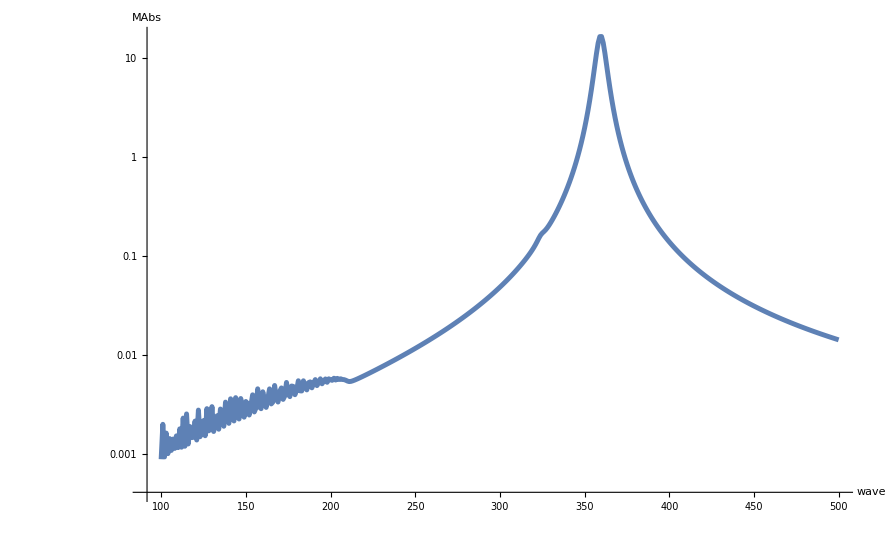

```mathematica
ListLogPlot[{MAbs},PlotStyle->{Thickness[0.004],Thickness[0.004]},AxesLabel->{ToString[condlmbdeV],SymbolName[Unevaluated[MAbs]]},LabelStyle->Directive[{Black,Bold,FontSize->18}],Joined->True,PlotRange->{Full,Full}]
```

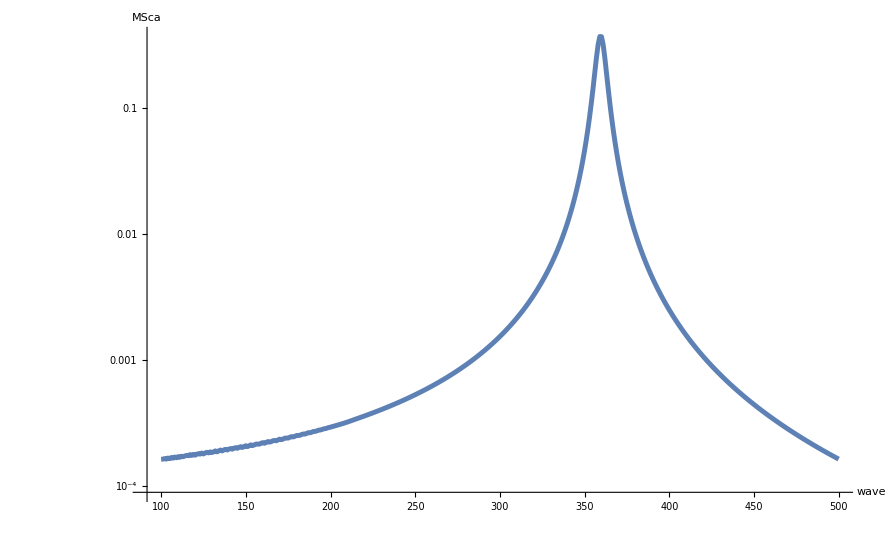

```mathematica
ListLogPlot[{MSca},PlotStyle->{Thickness[0.004],Thickness[0.004]},AxesLabel->{ToString[condlmbdeV],SymbolName[Unevaluated[MSca]]},LabelStyle->Directive[{Black,Bold,FontSize->18}],Joined->True,PlotRange->{Full,Full}]
```

```mathematica
Export["C:\\Users\\User\\OneDrive - Fondazione Istituto Italiano Tecnologia\\Model repository\\Henrikh\\mathematica_code_LRA_Drude_TF\\Abs.csv",MAbs]
```

C:\Users\User\OneDrive - Fondazione Istituto Italiano Tecnologia\Model repository\Henrikh\mathematica_code_LRA_Drude_TF\Abs.csv

```mathematica
Export["C:\\Users\\User\\OneDrive - Fondazione Istituto Italiano Tecnologia\\Model repository\\Henrikh\\mathematica_code_LRA_Drude_TF\\Sca.csv",MSca]
```

C:\Users\User\OneDrive - Fondazione Istituto Italiano Tecnologia\Model repository\Henrikh\mathematica_code_LRA_Drude_TF\Sca.csv